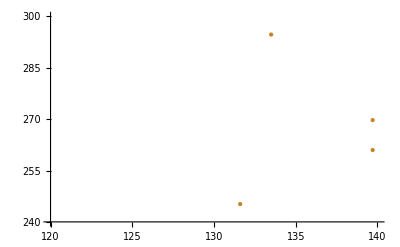

```mathematica
p2=ListPlot[
{Transpose@{(snuLSP@file10)[[;;,3,5,1]],(snuLSP@file10)[[;;,3,6,5]]},
Transpose@{(snuLSP@file10)[[;;,3,5,1]],(snuLSP@file10)[[;;,3,6,6]]},
Transpose@{(snuLSP@file10)[[;;,3,5,1]],(snuLSP@file10)[[;;,3,6,4]]}
},
ImageSize->400,
PlotRange->{{120,140},{240,300}},
PlotStyle->ColorData[31,"ColorList"][[{5}]],
TicksStyle->Medium]
```

```mathematica
Export["/Users/ruppell/Desktop/130GeVphotonLine.eps",p2,"EPS"]
```

/Users/ruppell/Desktop/130GeVphotonLine.eps

```mathematica
{pName[[{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]}~Join~(selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[;;,2,{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]//TableForm
```

M0 | MNR | tanβ | vevS | AlambdaN | lambda | lambdaN | kappa | PhisPI | Phi2PI | ksi | Alambda | Akappa | mh1 | mh2 | mS
148.299 | 127.422 | 25.9671 | 2841.8 | -967.292 | 0.143279 | 0.411272 | 0.0481597 | 3.17068 | 3.10577 | 252.088 | 1906.68 | -13.5557 | 4310.4 | 0.+334.154 ⅈ | 0.+184.933 ⅈ

```mathematica
(selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,3]]//TableForm
```

-271.796 | 291.625 | 400.636 | -413.745 | 619.57 |  |  | 
393.567 | 619.484 |  |  |  |  |  | 
0 | 4331.38 |  |  |  |  |  | 
-8.8×10^-14 | -2.361×10^-12 | 3.8502×10^-11 | -2337.5 |  |  |  | 
133.496 | 133.496 | 133.496 | 133.496 | 133.496 | 133.496 | 1702.98 | 2839.05
-0.0000863167 | 3.37903 | 125.811 | 294.71 | 4330.34 | 4330.35 |  | 
140.192 | 154.666 | 154.666 | 155.676 | 155.676 | 168.847 |  | 
998.556 | 999.357 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
814 | 1180.32 |  |  |  |  |  | 
988.651 | 1013.3 |  |  |  |  |  |

```mathematica
Dimensions@(selHiggsMass[240,250]@selSnuMass[130,135]@file10)
```

{1,10}

```mathematica
(selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,6]]
```

{0.0147898,~n1,27.483}

```mathematica
(Abs@((selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,4,3]]+I (selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,4,4]]))^2//MatrixForm
```

(0.0476826 | 0.952316
0.952318 | 0.0476828)

```mathematica
(Abs@((selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,4,5]]+I (selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,4,6]]))^2//MatrixForm
```

(0.103733 | 0.896267
0.896267 | 0.103734)

```mathematica
Chop[N@(selHiggsMass[290,300]@selSnuMass[130,135]@file10)[[1,4,9]]^2,0.01]//MatrixForm
```

(0 | 0 | 0 | 0 | 0.997238 | 0
0 | 0 | 0 | 0 | 0 | 0.999358
0 | 0.935168 | 0.0622318 | 0 | 0 | 0
0 | 0.0620628 | 0.93713 | 0 | 0 | 0
0.996956 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.996958 | 0 | 0)

```mathematica
Block[{mLSP,dm,sigma,LSPid,xeZ,xeA,assign,σ,σp,σn,mSnu,mChi,num,file,out},
xeZ=54;
xeA=131;
σn[name_]:=name[[;;,8,3,1]];
σp[name_]:=name[[;;,8,4,1]];
mSnu[name_]:=name[[;;,3,5,1]];
mChi[name_]:=Abs@name[[;;,3,1,1]];
assign[name_]:={mLSP,sigma,LSPid,dm}={
(Min/@Transpose@{mSnu@name,mChi@name}),
10^-36(xeZ Sqrt@σp@name+(xeA-xeZ)Sqrt@σn@name)^2/xeA^2,
If[#1=="~o1",1,2]&/@name[[;;,6,2]],
name[[;;,6,1]]
};
file = "/Users/ruppell/Math/temp/XenonTest.mc";
out=OpenWrite[file];
Write[out,OutputForm["<* assign@selHiggsMass[290,300]@selSnuMass[130,135]@file10; *>"]];
Do[
Write[out,OutputForm["<* mLSP[["<>ToString@num<>"]] *> <* sigma[["<>ToString@num<>"]] *> <* LSPid[["<>ToString@num<>"]] *> <* dm[["<>ToString@num<>"]] *>"]],
{num,1,First@Dimensions@selHiggsMass[290,300]@selSnuMass[130,135]@file10}
]
Close[file];
Splice[file,PageWidth->Infinity];
DeleteFile[file];
]
```